```mathematica
m[n_,z_]:=Pochhammer[z,n]/(n!)
bo2[z_,k_]:=Sum[m[k-2j,z]m[j,-z],{j,0,k/2}]
bo3[z_,k_]:=Sum[m[k-2j,z+1]m[j,-z],{j,0,k/2}]
bo3a[z_,k_]:=Sum[m[j,z]m[l,-z],{l,0,k/2},{j,0,k-2l}]
bo3b[z_,t_,k_]:=Sum[m[j,z]m[l,-z],{l,0,k/t},{j,0,k-t l}]
```

```mathematica
Table[bo3[k,j],{k,0,5},{j,0,k}]//Grid
```

1 |  |  |  |  | 
1 | 2 |  |  |  | 
1 | 3 | 4 |  |  | 
1 | 4 | 7 | 8 |  | 
1 | 5 | 11 | 15 | 16 | 
1 | 6 | 16 | 26 | 31 | 32

```mathematica
Table[Sum[Binomial[k,n],{n,0,j}],{k,0,5},{j,0,k}]//Grid
```

1 |  |  |  |  | 
1 | 2 |  |  |  | 
1 | 3 | 4 |  |  | 
1 | 4 | 7 | 8 |  | 
1 | 5 | 11 | 15 | 16 | 
1 | 6 | 16 | 26 | 31 | 32

```mathematica
Table[bo3[7.3,j],{j,0,8}]
```

{1,8.3,31.295,71.9195,115.591,144.414,155.463,157.515,157.592}

```mathematica
Table[Sum[Binomial[7.3,n],{n,0,j}],{j,0,8}]
```

{1.,8.3,31.295,71.9195,115.591,144.414,155.463,157.515,157.592}

```mathematica
bo2[2.3,2]
```

1.495

```mathematica
Binomial[2.3,2]
```

1.495

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
neg[n_,t_]:=1-t(Floor[n/t]-Floor[(n-1)/t])
al[n_,t_,0]:=UnitStep[n]
al[n_,t_,k_]:=al[n,t,k]=Sum[neg[j,t]/j al[n-j,t,k-1],{j,1,n}]
az[n_,t_,z_]:=Sum[z^k/k! al[n,t,k],{k,0,n}]
daz[n_,t_,z_]:=az[n,t,z]-az[n-1,t,z]
bn[z_,k_]:=daz[k,2,z]
```

```mathematica
Table[daz[n,2,3],{n,0,5}]
```

{1,3,3,1,0,0}

```mathematica
Table[bn[7,n],{n,0,7}]
```

{1,7,21,35,35,21,7,1}

```mathematica
(1+x)/(1+x/2)
```

(1+x)/(1+x/2)

```mathematica
D[bo3b[z,5,20],z]/.z->0
```

23502835/15519504

```mathematica
HarmonicNumber[20]-HarmonicNumber[Floor[20/5]]
```

23502835/15519504

```mathematica
D[az[20,5,z],z]/.z->0
```

23502835/15519504

```mathematica
al[20,5,1]
```

23502835/15519504

```mathematica
D[((1+x)/(1+x/2))^z,z]/.z->0
```

Log[(1+x)/(1+x/2)]

```mathematica
pri[n_]:=Sum[PrimePi[n^(1/k)]/k,{k,1,Log2@n}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]]bin[-z,p[[2]]],{p,FI[n]}]
```

```mathematica
po[n_,z_]:=Sum[dz[j,-z]dz[k,z],{j,1,n},{k,1,(n/j)^(1/2)}]
```

```mathematica
D[Expand@po[100,z],z]/.z->0
```

-116/5

```mathematica
pri[10]-pri[100]
```

-116/5

```mathematica
lo[n_,0]:=UnitStep[n-1]
lo[n_,k_]:=lo[n,k]=Sum[Abs[MoebiusMu[j]]lo[Floor[n/j],k-1],{j,2,n}]
lz[n_,z_]:=Sum[bin[z,k]lo[n,k],{k,0,Log2@n}]
lzd[n_,z_]:=Product[bin[z,p[[2]]],{p,FI[n]}]
lza[n_,z_]:=Sum[lzd[j,z],{j,1,n}]
```

```mathematica
Expand@lz[100,z]
```

1+(116 z)/5+(9389 z^2)/360+(395 z^3)/48+(347 z^4)/144+(17 z^5)/240+(7 z^6)/720

```mathematica
1+Integrate[D[(1+t)^z,t],{t,0,x}]+Integrate[D[(1+u)^-z,u],{u,0,x/2}]+Integrate[D[(1+t)^z,t]D[(1+u)^-z,u],{t,0,x},{u,0,(x-t)/2}]
```

ConditionalExpression[1-(1/z-(2^z (2+x)^-z)/z) z-2^z (1/(3+x))^z (3+x)^z z Beta[2/(3+x),1-z,z]+(3+x)^-z (1/(6+2 x))^-z z Beta[(2+x)/(3+x),1-z,z],Re[x]≥-1||x∉Reals]

```mathematica
FullSimplify[1-(1/z-(2^z (2+x)^-z)/z) z-2^z (1/(3+x))^z (3+x)^z z Beta[2/(3+x),1-z,z]+(3+x)^-z (1/(6+2 x))^-z z Beta[(2+x)/(3+x),1-z,z]]/.x->3/.z->2
```

Infinity::indet: Indeterminate expression 4/25 + ComplexInfinity + ComplexInfinity encountered.

Indeterminate

```mathematica
ab[x_,z_]:=1+Integrate[D[(1+t)^z,t],{t,0,x}]+Integrate[D[(1+u)^-z,u],{u,0,x/2}]+Integrate[D[(1+t)^z,t]D[(1+u)^-z,u],{t,0,x},{u,0,x/2}]
ab2[x_,z_]:=((1+x)/(1+x/2))^z
```

```mathematica
ab[6,.5]
```

1.32288

```mathematica
1+Integrate[D[(1+t)^z,t],{t,0,x}]+Integrate[D[(1+u)^-z,u],{u,0,x/2}]+Integrate[D[(1+t)^z,t]D[(1+u)^-z,u],{t,0,x},{u,0,x/2}]
```

ConditionalExpression[(1+x)^z+(2+x)^-z (-1+(1+x)^z) (2^z-(2+x)^z)-(1/z-(2^z (2+x)^-z)/z) z,Re[x]≥-1||x∉Reals]

```mathematica
FullSimplify[(1+x)^z+(2+x)^-z (-1+(1+x)^z) (2^z-(2+x)^z)-(1/z-(2^z (2+x)^-z)/z) z]
```

```mathematica
2^z ((1+x)/(2+x))^z/.x->113.3/.z->2.3
```

4.8269

```mathematica
((1+x)/(1+x/2))^z/.x->113.3/.z->2.3
```

4.8269

```mathematica
D[(1+t)^z,t]
```

(1+t)^(-1+z) z

```mathematica
D[(1+t)^-z,t]/.t->u
```

-(1+u)^(-1-z) z

```mathematica
FullSimplify[Integrate[LaguerreL[z-1,1,-t],{t,0,x}]]
```

-1+LaguerreL[z,-x]

```mathematica
FullSimplify@Integrate[LaguerreL[-z-1,1,-t],{t,0,x/2}]
```

ConditionalExpression[-1+Hypergeometric1F1[z,1,-x/2],Re[x]≥-2||x∉Reals]

```mathematica
Integrate[LaguerreL[z-1,1,-t]LaguerreL[-z-1,1,-u],{t,0,x},{u,0,(x-t)/2}]
```

∫_0^x z Hypergeometric1F1[1-z,2,-t] (-1+Hypergeometric1F1[z,1,(t-x)/2])ⅆt

```mathematica
FullSimplify@Table[1+(-1+LaguerreL[z,-x])+(-1+Hypergeometric1F1[z,1,-x/2])+∫_0^x z Hypergeometric1F1[1-z,2,-t] (-1+Hypergeometric1F1[z,1,(t-x)/2])ⅆt,{z,-3,3}]//TableForm
```

1/16 ⅇ^-x (14+2 ⅇ^x+(-10+x) x)
1/4 ⅇ^-x (3+ⅇ^x-x)
1/2 (1+ⅇ^-x)
1
2-ⅇ^(-x/2)
4-1/2 ⅇ^(-x/2) (6+x)
8-1/8 ⅇ^(-x/2) (56+x (16+x))

```mathematica
FullSimplify@Integrate[D[(1+t)^z,t],{t,0,x}]
```

ConditionalExpression[-1+(1+x)^z,Re[x]≥-1||x∉Reals]

```mathematica
FullSimplify@Integrate[D[(1+u)^-z,u],{u,0,x/2}]
```

ConditionalExpression[-1+2^z (2+x)^-z,Re[x]≥-2||x∉Reals]

```mathematica
FullSimplify@Integrate[D[(1+t)^z,t]D[(1+u)^-z,u],{t,0,x},{u,0,x/2}]
```

ConditionalExpression[(2+x)^-z (-1+(1+x)^z) (2^z-(2+x)^z),Re[x]≥-1||x∉Reals]

```mathematica
1+Integrate[D[(1+t)^z,t],{t,0,x}]+Integrate[D[(1+u)^-z,u],{u,0,x/k}]+Integrate[D[(1+t)^z,t]D[(1+u)^-z,u],{t,0,x},{u,0,x/k}]
```

ConditionalExpression[1+((k+x)/k)^-z (-1+(1+x)^z)-(1/z-((k+x)/k)^-z/z) z,(Re[x]≥-1||x∉Reals)&&((k≠0&&x≠0&&Re[k/x]≥0)||Re[k/x]≤-1||k/x∉Reals)]

```mathematica
FullSimplify[1+((k+x)/k)^-z (-1+(1+x)^z)-(1/z-((k+x)/k)^-z/z) z]/.x->8./.k->3./.z->2.3
```

7.88739

```mathematica
((1+x)/(1+x/k))^z/.x->8./.k->3./.z->2.3
```

7.88739

```mathematica
pz[x_,z_]:=Pochhammer[z,x]/x!
pk[x_,z_,k_]:=Sum[pz[t,z]pz[u,-z],{t,0,x},{u,0,(x-t)/k}]
pka[x_,z_,k_]:=Sum[pz[x-u k,z+1]pz[u,-z],{u,0,x/k}]
pkb[x_,z_,k_]:=Sum[pz[x-u k,-z+1]pz[u,z],{u,0,x/k}]
```

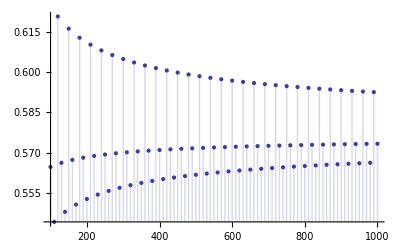

```mathematica
DiscretePlot[pka[n,z,3]/.z->-.5,{n,100,1000,10}]
```

```mathematica
2^(5.1+3I)
```

-16.7023+29.955 ⅈ

```mathematica
pka[30.,2.5,2]
```

5.65685

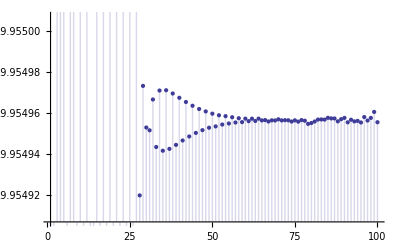

```mathematica
DiscretePlot[Im@pka[n,z,2]/.z->(5.1+3I),{n,1,100}]
```

```mathematica
bb[x_,z_]:=1+(-1+LaguerreL[z,-x])+(-1+Hypergeometric1F1[z,1,-x/2])+∫_0^x z Hypergeometric1F1[1-z,2,-t] (-1+Hypergeometric1F1[z,1,(t-x)/2])ⅆt
```

```mathematica
N[bb[58.,2.5+I]]
```

4.35147+3.61451 ⅈ

```mathematica
2^(2.5+I)
```

4.35147+3.61451 ⅈ

```mathematica
Limit[((1+x)/(1+x/k))^z,x->Infinity]
```

k^z

```mathematica
FullSimplify[Integrate[LaguerreL[z-1,1,-Log[t]],{t,1,x}]]
```

∫_1^x LaguerreL[-1+z,1,-Log[t]]ⅆt

```mathematica
FullSimplify@Integrate[LaguerreL[-z-1,1,-Log[u]],{u,1,x^(1/2)}]
```

∫_1^(√x) -z Hypergeometric1F1[1+z,2,-Log[u]]ⅆu

```mathematica
Integrate[LaguerreL[z-1,1,-Log[t]]LaguerreL[-z-1,1,-Log[u]],{t,1,x},{u,1,(x/t)^(1/2)}]
```

∫_1^x (-1+LaguerreL[z,1/2 Log[x/t]]) LaguerreL[-1+z,1,-Log[t]]ⅆt

```mathematica
cc[x_,z_]:=1+∫_1^x LaguerreL[-1+z,1,-Log[t]]ⅆt+∫_1^(√x) -z Hypergeometric1F1[1+z,2,-Log[u]]ⅆu+∫_1^x (-1+LaguerreL[z,1/2 Log[x/t]]) LaguerreL[-1+z,1,-Log[t]]ⅆt
```

```mathematica
FullSimplify@cc[x,1]
```

ConditionalExpression[(1+x)/2,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@cc[x,2]
```

ConditionalExpression[1/4 (1+3 x+x Log[x]),Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@cc[x,3]
```

ConditionalExpression[1/16 (2+14 x+x Log[x] (10+Log[x])),Re[x]≥0||x∉Reals]

```mathematica
pkk[x_,z_,k_]:=Sum[pz[t,2z]pz[u,-z]pz[v,-z],{t,0,x},{u,0,(x-t)/k},{v,0,(x-t-k u)/k}]
```

```mathematica
pkk[20.,2.6,2]
```

36.7583

```mathematica
4^(2.6)
```

36.7583

```mathematica
FullSimplify[Sum[Pochhammer[-z,u]/u!,{u,0,Floor[(x-t)/t]}]]
```

Gamma[-z+Floor[x/t]]/(Gamma[1-z] Gamma[Floor[x/t]])

```mathematica
Sum[Gamma[-z+Floor[x/t]]/(Gamma[1-z] Gamma[Floor[x/t]]),{t,0,x}]
```

∑_(t=0)^x Gamma[-z+Floor[x/t]]/(Gamma[1-z] Gamma[Floor[x/t]])

```mathematica
Sum[Gamma[-z+x/t]/(Gamma[1-z] Gamma[x/t]),{t,0,x}]
```

∑_(t=0)^x Gamma[x/t-z]/(Gamma[x/t] Gamma[1-z])

```mathematica
Expand@FullSimplify[(1-x^4)/(1-x)]
```

1+x+x^2+x^3

```mathematica
(1-x^k)/(1-x)
```

(1-x^k)/(1-x)

```mathematica
(1+x)/(1+x/k)
```

(1+x)/(1+x/k)

```mathematica
pz[x_,z_]:=Pochhammer[z,x]/x!
pt[x_,z_,a_]:=If[x/a<1,1,Sum[pz[j,z]pt[x-a j,z,a+1],{j,0,x/a}]]
```

```mathematica
D[Expand@pt[20,z,1],z]/.z->0
```

7257705647/232792560

```mathematica
Sum[PartitionsP[j],{j,0,20}]
```

2714

```mathematica
Sum[HarmonicNumber[Floor[20/k]],{k,1,20}]
```

7257705647/232792560

```mathematica
FullSimplify@Expand[x/(1-x-x^2)/.x->(1+x)]
```

-(1+x)/(1+x (3+x))

```mathematica
Sum[Fibonacci[k]x^k,{k,0,Infinity}]
```

-x/(-1+x+x^2)

```mathematica
Table[D[x/(1-x-x^2),{x,k}]/k!/.x->0,{k,0,20}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
FullSimplify[1-x-x^2]
```

1-x (1+x)

```mathematica
Sum[Binomial[z,k](-1)^k x^k,{k,0,Infinity}]
```

(1-x)^z

```mathematica
fl[j_,k_]:=1-k(Floor[j/k]-Floor[(j-1)/k])
tri[z_,x_]:=Sum[pz[x-3 u,z]pz[u,-z],{u,0,x/3}]
```

```mathematica
Table[tri[4,k],{k,0,12}]
```

{1,4,10,16,19,16,10,4,1,0,0,0,0}

```mathematica
tt[z_]:=Sum[tri[z,k] x^k,{k,0,10}]
```

```mathematica
tt[1]
```

-1+x-x^2

```mathematica
(* http://oeis.org/A001350 *)
Clear[am,amm]
am[n_,0]:=UnitStep[n]
am[n_,k_]:=am[n,k]=Sum[Fibonacci[j]am[n-j,k-1],{j,1,n}]
amz[n_,z_]:=Sum[bin[z,k]am[n,k],{k,0,n}]
damz[n_,z_]:=amz[n,z]-amz[n-1,z]
iv[n_]:=Floor[n/2]-Floor[(n+1)/2]
amm[n_,0]:=UnitStep[n]
amm[n_,k_]:=amm[n,k]=Sum[iv[j]amm[n-j,k-1],{j,1,n}]
ammz[n_,z_]:=Sum[bin[z,k]amm[n,k],{k,0,n}]
dammz[n_,z_]:=amz[n,z]-ammz[n-1,z]

Table[D[amz[j,z],z]/.z->0,{j,1,10}]
Table[D[damz[j,z],z]/.z->0,{j,1,10}]
Table[damz[j,z]/.z->-1,{j,1,32}]
Table[ammz[j,z]/.z->-1,{j,1,32}]
```

{1,3/2,17/6,49/12,377/60,179/20,1833/140,5241/280,68449/2520,98941/2520}

{1,1/2,4/3,5/4,11/5,8/3,29/7,45/8,76/9,121/10}

{-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0,-1,0}

{2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887}

```mathematica
damz[10,1]
```

55

```mathematica
Fibonacci[10]
```

55

```mathematica
377*2
```

754

```mathematica
Table[iv[n],{n,1,10}]
```

{-1,0,-1,0,-1,0,-1,0,-1,0}